### Plots showing the relative error of a stirling approximation.

```mathematica
<<peeters`;
peeters`setGitDir["../project/figures/phy452-basicstatmech"]
```

/Users/pjoot/project/figures/phy452-basicstatmech

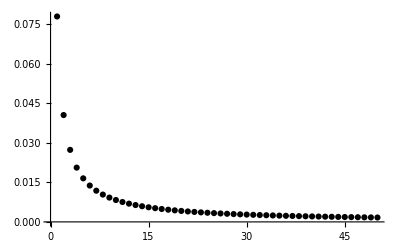

```mathematica
Clear[stirling, stirlingErrorFig3]
stirling[N_] = Sqrt[2 Pi N] N^N E^(-N) ;
(*stirling[n] // TraditionalForm*)
stirlingErrorFig3 = Module[{s,f, r, p},
r = 50 ;
s = Table[{n, stirling[n]}, {n, 1, r}] // N ;
f = Table[{n, Factorial[n]}, {n, 1, r}] // N  ;
d = Table[(Factorial[n] - stirling[n])/Factorial[n], {n, 1, r}]  // N ;
 p = ListPlot[d, 
PlotRange -> Full,
PlotStyle->{Thick,Black},
 AxesLabel->{
MaTeX["N"],
MaTeX["1 -\\frac{\\sqrt{2 \\pi N}}{N!} e^{-N} N^{N}"]
}] ;
(* {d, p} *)
p
]
(*stirling[1] // N*)
```

```mathematica
peeters`exportForLatex["stirlingErrorFig3", stirlingErrorFig3]
```

{stirlingErrorFig3.eps,stirlingErrorFig3pn.png}